## Reproduce Raffelt’s Paper

Linearized Eqn

```mathematica
a={{s,S},{Conjugate@S,-s}}
b={{sp,Sp},{Conjugate@Sp,-sp}}
```

{{s,S},{Conjugate[S],-s}}

{{sp,Sp},{Conjugate[Sp],-sp}}

```mathematica
a.b-b.a//FullSimplify//MatrixForm
```

(-Sp Conjugate[S]+S Conjugate[Sp] | -2 S sp+2 s Sp
2 sp Conjugate[S]-2 s Conjugate[Sp] | Sp Conjugate[S]-S Conjugate[Sp])

```mathematica
1/2{{1,S},{Conjugate@S, -1}}.{{h11,h12},{Conjugate@h12,h22}}/2-1/2{{h11,h12},{Conjugate@h12,h22}}.{{1,S},{Conjugate@S, -1}}/2//Simplify//MatrixForm
```

(1/4 (S Conjugate[h12]-h12 Conjugate[S]) | 1/4 (2 h12+(-h11+h22) S)
1/4 (-2 Conjugate[h12]+(h11-h22) Conjugate[S]) | 1/4 (-S Conjugate[h12]+h12 Conjugate[S]))

Polarization Tensor

A axial symmetric case

Parameters

```mathematica
G1=0.5;
G2=0.5;
```

```mathematica
eta=DiagonalMatrix[{1,-1,-1,-1}];
%//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
v[theta_,phi_]:={1,Cos[theta]Sin[phi],Sin[theta]Sin[phi],Cos[phi]}
kno[nIndex_,theta_,phi_]:={1,nIndex Cos[theta]Sin[phi],nIndex Sin[theta]Sin[phi],nIndex Cos[phi]}
k[omega_,nIndex_,theta_,phi_]:=omega kno[nIndex,theta,phi]
```

```mathematica
vvMatrix[theta_,phi_]=Outer[Times,v[theta,phi],v[theta,phi]];
%//MatrixForm
```

(1 | Cos[theta] Sin[phi] | Sin[phi] Sin[theta] | Cos[phi]
Cos[theta] Sin[phi] | Cos[theta]^2 Sin[phi]^2 | Cos[theta] Sin[phi]^2 Sin[theta] | Cos[phi] Cos[theta] Sin[phi]
Sin[phi] Sin[theta] | Cos[theta] Sin[phi]^2 Sin[theta] | Sin[phi]^2 Sin[theta]^2 | Cos[phi] Sin[phi] Sin[theta]
Cos[phi] | Cos[phi] Cos[theta] Sin[phi] | Cos[phi] Sin[phi] Sin[theta] | Cos[phi]^2)

```mathematica
kno[omega,nIndex,thetaK,phiK].v[theta,phi]
kno[omega,nIndex,0,0].v[theta,phi]
kno[omega,nIndex,0,0]
```

kno[omega,nIndex,thetaK,phiK].{1,Cos[theta] Sin[phi],Sin[phi] Sin[theta],Cos[phi]}

kno[omega,nIndex,0,0].{1,Cos[theta] Sin[phi],Sin[phi] Sin[theta],Cos[phi]}

kno[omega,nIndex,0,0]

Define the N Matrix without integral. I leave the integral to numerical calculations.

```mathematica
nMatrix1[theta1_,phi_,nIndex_,thetaK_,phiK_]:=(1/(kno[nIndex,thetaK,phiK].eta.v[theta1,phi])) G1 vvMatrix[theta1,phi]//FullSimplify
nMatrix2[theta2_,phi_,nIndex_,thetaK_,phiK_]:=(1/(kno[nIndex,thetaK,phiK].eta.v[theta2,phi])) G2 vvMatrix[theta2,phi]//FullSimplify
```

```mathematica
nMatrix1[theta1,phi,nIndex,thetaK,phiK]//MatrixForm
```

(0.5/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[theta1] Sin[phi])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Sin[phi] Sin[theta1])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[phi])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK])
(0.5 Cos[theta1] Sin[phi])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[theta1]^2 Sin[phi]^2)/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[theta1] Sin[phi]^2 Sin[theta1])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[phi] Cos[theta1] Sin[phi])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK])
(0.5 Sin[phi] Sin[theta1])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[theta1] Sin[phi]^2 Sin[theta1])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Sin[phi]^2 Sin[theta1]^2)/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[phi] Sin[phi] Sin[theta1])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK])
(0.5 Cos[phi])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[phi] Cos[theta1] Sin[phi])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[phi] Sin[phi] Sin[theta1])/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]) | (0.5 Cos[phi]^2)/(-1.+nIndex Cos[phi] Cos[phiK]+nIndex Cos[theta1-thetaK] Sin[phi] Sin[phiK]))

## Axial Symmetric Case

To calculate the values, I have to choose a specific direction of k.

thetaK=0
phiK=0

First of all we find the polarization tensor for this specific case

```mathematica
nMatrixPart1[theta_]=Assuming[-1<Re[n]<0||0<Re[n]<1||n∉Reals,
Integrate[1/(1-n Cos[phi]) vvMatrix[theta,phi],{phi,0,2Pi}]
]
```

{{(2 (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))]))/(√(-1+n^2)),0,0,-(2 (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n √(-1+n^2))},{0,(2 Cos[theta]^2 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])))/n^2,((π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[2 theta])/n^2,0},{0,((π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[2 theta])/n^2,(2 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[theta]^2)/n^2,0},{-(2 (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n √(-1+n^2)),0,0,-(2 (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n^2 √(-1+n^2))}}

N matrix becomes

```mathematica
nMatrixAS[n_,theta1_,theta2_]=G1 nMatrixPart1[theta1]+G2 nMatrixPart1[theta2];
%//MatrixForm
```

((2. (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))]))/(√(-1+n^2)) | 0. | 0. | -(2. (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n √(-1+n^2))
0. | (1. Cos[theta1]^2 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])))/n^2+(1. Cos[theta2]^2 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])))/n^2 | (0.5 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[2 theta1])/n^2+(0.5 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[2 theta2])/n^2 | 0.
0. | (0.5 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[2 theta1])/n^2+(0.5 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[2 theta2])/n^2 | (1. (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[theta1]^2)/n^2+(1. (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[theta2]^2)/n^2 | 0.
-(2. (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n √(-1+n^2)) | 0. | 0. | -(2. (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n^2 √(-1+n^2)))

Polarization tensor becomes

```mathematica
polarizationTensorSA[omega_,n_,theta1_,theta2_]:=eta omega + nMatrixAS[n,theta1,theta2]//Simplify
```

```mathematica
polarizationTensorSA[omega,n,theta1,theta2]//MatrixForm
```

(omega+(2. (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))]))/(√(-1+n^2)) | 0. | 0. | -(2. (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n √(-1+n^2))
0. | -omega+(1. Cos[theta1]^2 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])))/n^2+(1. Cos[theta2]^2 (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])))/n^2 | (0.5 (π+√(-1+n^2) Log[-(1+n)/(√(-1+n^2))]-1. √(-1+n^2) Log[(1+n)/(√(-1+n^2))]) (2. Cos[theta1] Sin[theta1]+2. Cos[theta2] Sin[theta2]))/n^2 | 0.
0. | (0.5 (π+√(-1+n^2) Log[-(1+n)/(√(-1+n^2))]-1. √(-1+n^2) Log[(1+n)/(√(-1+n^2))]) (2. Cos[theta1] Sin[theta1]+2. Cos[theta2] Sin[theta2]))/n^2 | -omega+(1. (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[theta1]^2)/n^2+(1. (π+√(-1+n^2) (Log[-(1+n)/(√(-1+n^2))]-Log[(1+n)/(√(-1+n^2))])) Sin[theta2]^2)/n^2 | 0.
-(2. (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n √(-1+n^2)) | 0. | 0. | -omega-(2. (√(-1+n^2) π-Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))]))/(n^2 √(-1+n^2)))

```mathematica
drFun[nIndex_]:=Module[{thetaKM,phiKM,theta1M,theta2M,polMatrixM,eqnM},

thetaKM=0;
phiKM=0;

theta1M=ArcCos@0.9;
theta2M=ArcCos@0.3;


polMatrixM=polarizationTensorSA[omega,nIndex,theta1M,theta2M];

Det@polMatrixM==0
]
```

```mathematica
drFun[n]
```

1/(n^7 (-1+n^2))3.82738×10^-18 (-12.5664 n (-1.20275×10^17 (3.14159+1. √(-1+n^2) Log[-(1+n)/(√(-1+n^2))]-1. √(-1+n^2) Log[(1+n)/(√(-1+n^2))])^2+2.61276×10^17 (-2.82743+1. n^2 omega-0.9 √(-1+n^2) Log[-(1+n)/(√(-1+n^2))]+0.9 √(-1+n^2) Log[(1+n)/(√(-1+n^2))]) (-3.45575+1. n^2 omega-1.1 √(-1+n^2) Log[-(1+n)/(√(-1+n^2))]+1.1 √(-1+n^2) Log[(1+n)/(√(-1+n^2))])) (1. √(-1+n^2)-0.31831 Log[-(2 (1+n))/(√(-1+n^2))]+0.31831 Log[(2 (1+n))/(√(-1+n^2))]) (√(-1+n^2) π-1. Log[-(2 (1+n))/(√(-1+n^2))]+Log[(2 (1+n))/(√(-1+n^2))])-1. n (√(-1+n^2) omega+2. Log[-(1+n)/(√(-1+n^2))]-2. Log[(1+n)/(√(-1+n^2))]) (-1.20275×10^17 (3.14159+1. √(-1+n^2) Log[-(1+n)/(√(-1+n^2))]-1. √(-1+n^2) Log[(1+n)/(√(-1+n^2))])^2+2.61276×10^17 (-2.82743+1. n^2 omega-0.9 √(-1+n^2) Log[-(1+n)/(√(-1+n^2))]+0.9 √(-1+n^2) Log[(1+n)/(√(-1+n^2))]) (-3.45575+1. n^2 omega-1.1 √(-1+n^2) Log[-(1+n)/(√(-1+n^2))]+1.1 √(-1+n^2) Log[(1+n)/(√(-1+n^2))])) (6.28319 √(-1+n^2)+1. n^2 √(-1+n^2) omega-2. Log[-(2 (1+n))/(√(-1+n^2))]+2. Log[(2 (1+n))/(√(-1+n^2))]))==0

```mathematica
listofkz=Table[nIndex,{nIndex,-0.99,0.99,0.009}];
```

```mathematica
pltDataC1=Table[
Table[{n,1}omega/.NSolve[drFun[n],omega][[i]],{n,listofkz}],
{i,1,4}];
```

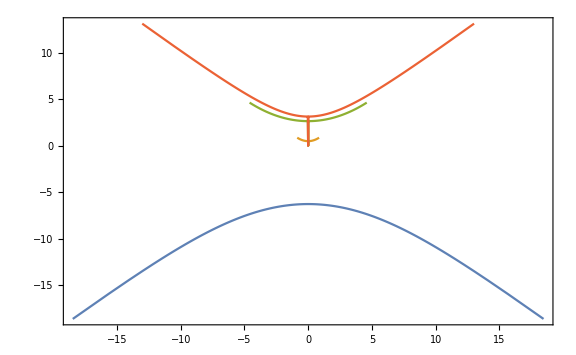

```mathematica
ListPlot[pltDataC1,PlotRange->Full,Joined->True,Frame->True,ImageSize->Large]
```